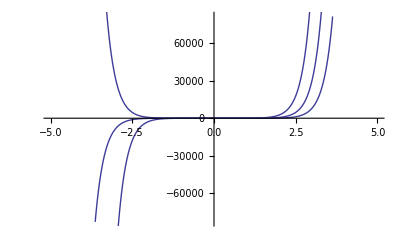

```mathematica
Show[Plot[f[x],{x,-5,5}],Plot[f'[x],{x,-5,5}],Plot[f''[x],{x,-5,5}]]
```

```mathematica
f[x_]:=(x^2-1)(Sinh[x])^3;
```

```mathematica
f[x_]:=x^2;
```

```mathematica
f[0]
```

0

```mathematica
(*a,b przedzial*)
```

```mathematica
Sieczne[a_,b_,iter_]:=Module[{x=Table[0&,{iter}],x1,x2,i, h=Random[Real,{a,b}]} ,

Print["Warunek na zgodnosc znakow pochodnych: ",f'[h]*f''[h]];
If[f'[h]*f''[h]>=0,
x1=a;
Print["x1= ",x1];
Print["x2=", x2=N[x1-f[x1]/(f[b]-f[x1])(b-x1)]];
x_⟦1⟧=x1;
x_⟦2⟧=x2;
For[i=3,i≤iter,i++,
x_⟦i⟧=x_⟦i-1⟧-(f[x_⟦i-1⟧](x_⟦i-1⟧-x_⟦i-2⟧))/(f[x_⟦i-1⟧]-f[x_⟦i-2⟧])
]Print["Miejsce zerowe z dokladnoscia do 10^-8: x= ",x_⟦iter⟧]
(*jesli nie*),
x1=b;
Print["x1= ",x1];
Print["x2=", x2=N[x1-f[x1]/(f[a]-f[x1])(a-x1)]];
x_⟦1⟧=x1;
x_⟦2⟧=x2;
For[i=3,i≤iter,i++,
x_⟦i⟧=x_⟦i-1⟧-(f[x_⟦i-1⟧](x_⟦i-1⟧-x_⟦i-2⟧))/(f[x_⟦i-1⟧]-f[x_⟦i-2⟧])
]Print["Miejsce zerowe z dokladnoscia do 10^-8: x= ",x_⟦iter⟧]
]Return[];];
```

```mathematica
Sieczne[0.00001,0.999,23]
```

Warunek na zgodnosc znakow pochodnych: 0.197478

x1= 0.00001

x2=0.00001

Miejsce zerowe z dokladnoscia do 10^-8: x= 2.48511×10^-8